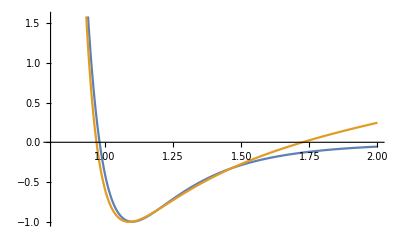

```mathematica
Plot[{(1.1/r)^12-2(1.1/r)^6,(1.1/((r-1.1)*2.5+1.1))^4-2(1.1/((r-1.1)*2.5+1.1))^2+.5*r-.5*1.1},{r,0.8,2.0}]
```

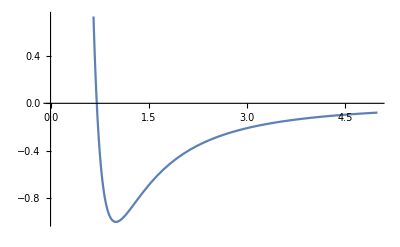

```mathematica
Plot[(1/r)^4-2(1/r)^2,{r,0,5.0}]
```

```mathematica
(m/((r-m)*3+m))^4-2(m/((r-m)*3+m))^2//FullSimplify
```

```mathematica
(m^2 (m^2-2 (2 m-3 r)^2))/(2 m-3 r)^4/.{m->1.1}
```

(1.21 (1.21-2 (2.2-3 r)^2))/(2.2-3 r)^4

```mathematica
(m/r)^12-2(m/r)^6//FullSimplify
```

(m^6 (m^6-2 r^6))/r^12

```mathematica
(m/r)^4-2(m/r)^2//FullSimplify
```

(m^4-2 m^2 r^2)/r^4

```mathematica
D[(m/(√(x^2+y^2)))^4-2(m/(√(x^2+y^2)))^2,x]//FullSimplify
```

(4 m^2 x (-m^2+x^2+y^2))/((x^2+y^2)^3)

```mathematica
(1/r)^2-2(1/r)/.{r->0.45}
```

0.493827

```mathematica
(1/r)^2-2(1/r)/.{r->2.}
```

-0.75

```mathematica
D[(1/r)^2-2(1/r),r]/.{r->2}
```

1/4

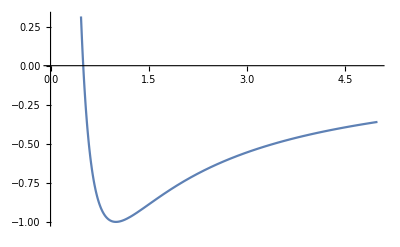

```mathematica
Plot[(1/r)^2-2(1/r),{r,0,5.0}]
```

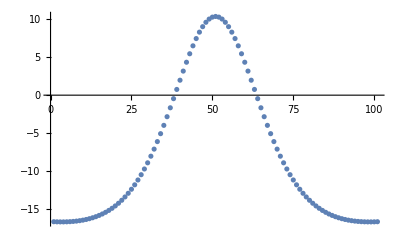

```mathematica
{-16.646,-16.661,-16.669,-16.668,-16.658,-16.638,-16.607,-16.565,-16.509,-16.438,-16.352,-16.248,-16.126,-15.983,-15.817,-15.626,-15.408,-15.160,-14.881,-14.567,-14.215,-13.823,-13.387,-12.906,-12.375,-11.792,-11.155,-10.462,-9.7097,-8.8982,-8.0268,-7.0961,-6.1076,-5.0644,-3.9709,-2.8334,-1.6599,-0.46033,0.75336,1.9673,3.1657,4.3313,5.4457,6.4897,7.4438,8.2893,9.0084,9.5856,10.008,10.265,10.352,10.265,10.008,9.5856,9.0084,8.2893,7.4438,6.4897,5.4457,4.3313,3.1657,1.9673,0.75336,-0.46033,-1.6599,-2.8334,-3.9709,-5.0644,-6.1076,-7.0961,-8.0268,-8.8982,-9.7097,-10.462,-11.155,-11.792,-12.375,-12.906,-13.387,-13.823,-14.215,-14.567,-14.881,-15.160,-15.408,-15.626,-15.817,-15.983,-16.126,-16.248,-16.352,-16.438,-16.509,-16.565,-16.607,-16.638,-16.658,-16.668,-16.669,-16.661,-16.646}//ListPlot
```

```mathematica
peaks[x_,y_]:=3*(1-x)^2*Exp[-x^2-(y+1)^2]-10*(x/5-x^3-y^5)*Exp[-x^2-y^2]-1/3*Exp[-(x+1)^2-y^2];
```

```mathematica
FindMinimum[peaks[x,y],{{x,-1},{y,0}}][[2]][[All,2]]
```

{-1.3474,0.204519}

```mathematica
FindMinimum[peaks[x,y],{{x,0},{y,-2}}][[2]][[All,2]]
```

{0.228279,-1.62553}

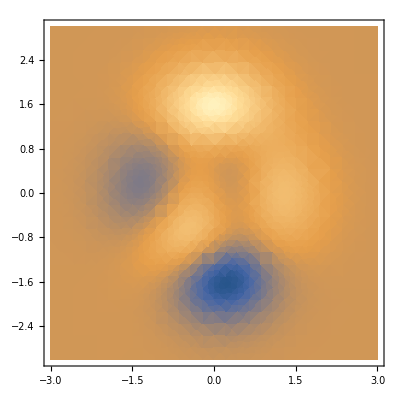

```mathematica
DensityPlot[peaks[x,y],{x,-3,3},{y,-3,3},PlotRange->Full]
```

```mathematica
Solve[D[peaks[x,y],x]==0&&D[peaks[x,y],y]==0,{x,y}]
```

$Aborted

```mathematica
D[peaks[x,y],x]
```

-6 ⅇ^(-x^2-(1+y)^2) (1-x)-6 ⅇ^(-x^2-(1+y)^2) (1-x)^2 x+2/3 ⅇ^(-(1+x)^2-y^2) (1+x)-10 ⅇ^(-x^2-y^2) (1/5-3 x^2)+20 ⅇ^(-x^2-y^2) x (x/5-x^3-y^5)

```mathematica
D[peaks[x,y],y]
```

2/3 ⅇ^(-(1+x)^2-y^2) y+50 ⅇ^(-x^2-y^2) y^4-6 ⅇ^(-x^2-(1+y)^2) (1-x)^2 (1+y)+20 ⅇ^(-x^2-y^2) y (x/5-x^3-y^5)